```mathematica
SystemInformation[]
```

1234567

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

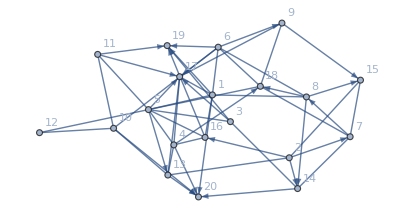

```mathematica
randomWeightedMixedGraph=RandomWeightedMixedGraph[{20,54},0.68,RandomReal[]&,VertexLabels->Automatic]
```

```mathematica
EdgeList[randomWeightedMixedGraph,_<->_]
```

{1<->8,1<->16,3<->5,4<->13,4<->17,5<->11,5<->16,5<->18,6<->10,6<->18,7<->14,7<->15,7<->18,9<->17,9<->18,10<->11,10<->13,13<->17}

```mathematica
EdgeList[randomWeightedMixedGraph,_<->_]/.{u_<->v_->Sequence@@{u->v,v->u}}
```

{1->8,8->1,1->16,16->1,3->5,5->3,4->13,13->4,4->17,17->4,5->11,11->5,5->16,16->5,5->18,18->5,6->10,10->6,6->18,18->6,7->14,14->7,7->15,15->7,7->18,18->7,9->17,17->9,9->18,18->9,10->11,11->10,10->13,13->10,13->17,17->13}

```mathematica
Graph[Join[EdgeList[randomWeightedMixedGraph,_<->_]/.{u_<->v_->Sequence@@{u->v,v->u}},EdgeList[randomWeightedMixedGraph,_DirectedEdge]]]
```

-Graphics-

```mathematica
FindPostmanTour[Graph[Join[EdgeList[randomWeightedMixedGraph,_<->_]/.{u_<->v_->Sequence@@{u->v,v->u}},EdgeList[randomWeightedMixedGraph,_DirectedEdge]]]]
```

{}

```mathematica
FindEulerianCycle[Graph[Join[EdgeList[randomWeightedMixedGraph,_<->_]/.{u_<->v_->Sequence@@{u->v,v->u}},EdgeList[randomWeightedMixedGraph,_DirectedEdge]]]]
```

{}

```mathematica
EulerizeGraph[Graph[Join[EdgeList[randomWeightedMixedGraph,_<->_]/.{u_<->v_->Sequence@@{u->v,v->u}},EdgeList[randomWeightedMixedGraph,_DirectedEdge]]]]
```

EulerizeGraph[-Graphics-]

```mathematica
Names["Edge*"]
```

{EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeCapForm,EdgeChromaticNumber,EdgeColor,EdgeConnectivity,EdgeContract,EdgeCost,EdgeCount,EdgeCoverQ,EdgeCycleMatrix,EdgeDashing,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeList,EdgeOpacity,EdgeQ,EdgeRenderingFunction,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeTaggedGraph,EdgeTaggedGraphQ,EdgeTags,EdgeThickness,EdgeTransitiveGraphQ,EdgeValueRange,EdgeValueSizes,EdgeWeight,EdgeWeightedGraphQ}

```mathematica
?EulerizeGraph
```

```mathematica
NestWhile[Function[x,EdgeAdd[x,(First[#1]->Last[#1]&)[First[TakeDrop[Select[VertexList[x],OddQ[VertexDegree[x,#1]]&],2]]]]],-Graphics-,!EulerianGraphQ[#1]&]
```

TakeDrop::iseq: Invalid sequence specification 2 for an expression of length 0.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

TakeDrop::iseq: Invalid sequence specification 2 for an expression of length 0.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

TakeDrop::iseq: Invalid sequence specification 2 for an expression of length 0.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

$Aborted